# Ordinary Differential Eqautios

## Geometrical View of ODEs

### Example 1

Consider the ODE: y'=y-x^2 with solution:

```mathematica
DSolve[y'[x]==y[x]-x^2,y[x],x][[1,1]]/.C[1]->c
```

y[x]→2+c ⅇ^x+2 x+x^2

Draw the direction field and the integral curves

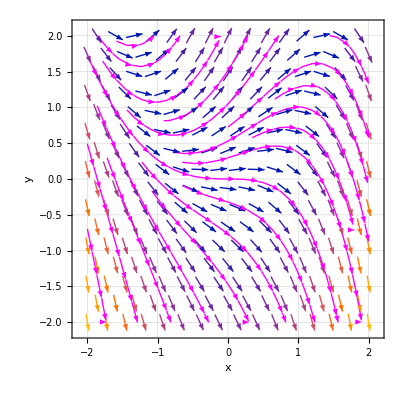

```mathematica
VectorPlot[{1,y-x^2},{x,-2,2},{y,-2,2},StreamPoints->Coarse,StreamColorFunction->None,StreamStyle->Magenta,FrameLabel->{"x","y"},GridLines->Automatic]
```

For a specific slope value c the isocline is given by y-x^2=c → y=c+x^2

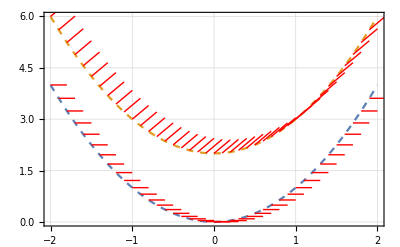

```mathematica
Isocline=Plot[{0+x^2,2+x^2},{x,-2,2},PlotStyle->Dashed,GridLines->Automatic,Frame->True];
LineElement0=Graphics[{Red,Line[Table[{{x,0+x^2},{x+0.2,0+x^2}},{x,-2,1.95,0.1}]]}];
LineElement1=Graphics[{Red,Line[Table[{{x,2+x^2},{x+0.2,2+x^2+0.4}},{x,-2,1.95,0.1}]]}];
IsoclinePlot=Show[Isocline,LineElement0,LineElement1]
```

Consider the ODE: y'=-x/y with solution:

```mathematica
DSolve[y'[x]==-x/y[x],y[x],x][[1,1]]/.C[1]->c
```

y[x]→-√(2 c-x^2)

Draw the direction field and the integral curves

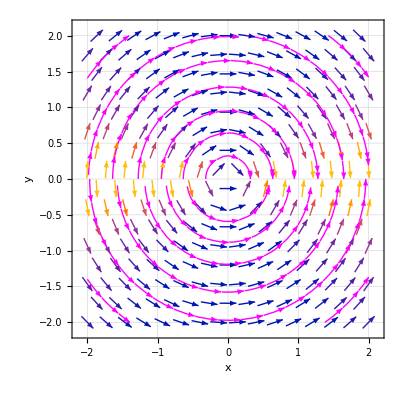

For a specific slope value c the isocline is given by -x/y=c → y=-x/c

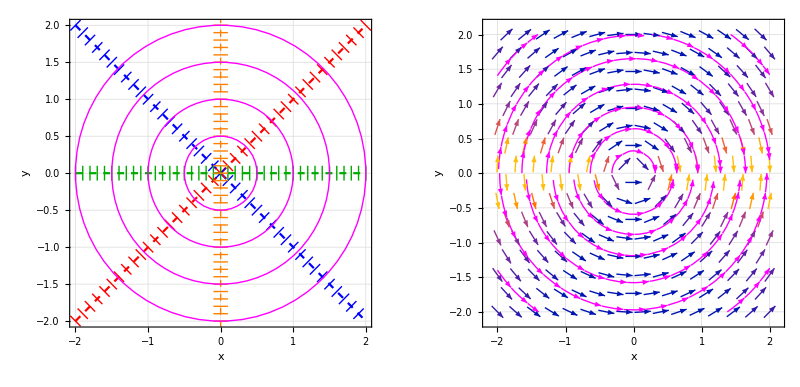

```mathematica
Isocline1=Plot[{-x/1},{x,-2,2},PlotStyle->{Dashed,Blue},Frame->True,GridLines->Automatic,FrameLabel->{"x","y"},AspectRatio->1];
Isocline2=Plot[{-x/-1},{x,-2,2},PlotStyle->{Dashed,Red}];
Isocline3=Plot[{-x/Infinity},{x,-2,2},PlotStyle->{Dashed,Darker[Green]}];
Isocline4=Graphics[{Dashed,Orange,Line[{{0,-2.1},{0,2.1}}]}];
LineElement1=Graphics[{Blue,Line[Table[{{x-0.1/(√2),-x/1-0.1/(√2)},{x+0.1/(√2),-x/1+0.1/(√2)}},{x,-2,1.95,0.1}]]}];
LineElement2=Graphics[{Red,Line[Table[{{x-0.1/(√2),-x/-1+0.1/(√2)},{x+0.1/(√2),-x/-1-0.1/(√2)}},{x,-2,2,0.1}]]}];
LineElement3=Graphics[{Darker[Green],Line[Table[{{x,-0.1},{x,0.1}},{x,-2,2,0.1}]]}];
LineElement4=Graphics[{Orange,Line[Table[{{-0.1,y},{0.1,y}},{y,-2.1,2.1,0.1}]]}];
IntegraLCurve=Graphics[{Magenta,Circle[{0,0},0.5],Circle[{0,0},1],Circle[{0,0},1.5],Circle[{0,0},2]}];
DirectionFieldManual=Show[Isocline1,Isocline2,Isocline3,Isocline4,LineElement1,LineElement2,LineElement3,LineElement4,IntegraLCurve];
DirectionFieldComputer=VectorPlot[{1,-x/y},{x,-2,2},{y,-2,2},StreamPoints->Coarse,StreamColorFunction->None,StreamStyle->Magenta,FrameLabel->{"x","y"},GridLines->Automatic];
GraphicsGrid[{{DirectionFieldManual,DirectionFieldComputer}}]
```